File::badfile: The specified argument  should be a valid string or File.

edge_states_ana_1.pdf

edge_states_ana_2.pdf

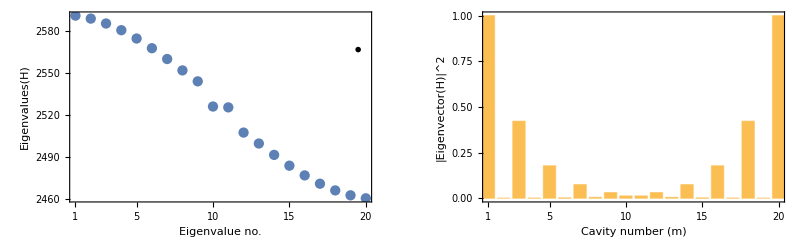

```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
texStyle={FontFamily->"Latin Modern Roman",FontSize->14,FontColor->Black};
SetOptions[ListPlot,BaseStyle->texStyle,Frame->True,Axes->False];
SetOptions[BarChart,BaseStyle->texStyle,Frame->True,Axes->False,FrameTicks->True];
eigenSystem[H_]:=Module[{λ,v,s},s=Eigensystem[H]//Transpose;
Transpose@SortBy[s,#[[1]]&]
]
δ=ωR-(ω0+ωv);
g=0.5;
ωR=2720;
ω00=2526;
ωv=194;
Γ=(γ0+γR+γv);
{γ0,γR,γv}={4,0.7,2.9};
G=g^2 Γ/(δ^2+Γ^2/4);
L=20;
Ω0=33;
δΩ=7;
{Ω1,Ω2}=(Ω0+# δΩ)&/@{-1,1};
band=Table[If[!EvenQ[n],Ω1,Ω2],{n,1,L-1}];
H=SparseArray[{Band[{1,1}]->ω00,Band[{2,1}]->band,Band[{1,2}]->band},{L,L}]//Normal//N;
BarChart[Abs[Eigenvectors[H][[10]]],ChartStyle->RGBColor[0.,0.67,0.1]];
circle=Graphics[{GrayLevel[0.5],Disk[]},ImageSize->9];
disk=Graphics[{Black,Disk[]},ImageSize->11];
ticks=Table[{x,If[MemberQ[{1,5,10,15,20},x],x,""]},{x,1,20}];
p1=ListPlot[Eigenvalues[H],Joined->False,GridLines->{None,{1}},PlotRangePadding->Scaled[.03],FrameLabel->{"Eigenvalue no.","Eigenvalues(H)"},ImageSize->Large,PlotMarkers->circle,PlotRange->{{1,20},Automatic},FrameTicks->{1,5,10,15,20}];
p2=ListPlot[Eigenvalues[H],PlotRangePadding->Scaled[.15],Joined->False,ColorFunctionScaling->False,ColorFunction->Function[{x,y},GrayLevel[1-6G/.ω0->y]],FrameLabel->{"Eigenvalue no.","Eigenvalues(H)"},PlotRange->{{1,20},Automatic}];
legend=ArrayPlot[{Table[x,{x,0,1,0.01}]}//Transpose,Mesh->None,AspectRatio->10,ColorFunction->GrayLevel,FrameTicks->{{None,Automatic},{None,None}},DataRange->{{1,2},{0,1}},ImageSize->20];
listplot=Show[p1,p2,ImagePadding->{{70,5},{50,5}},PlotRange->{{1,20},Automatic},FrameTicks->{ticks,Automatic},Epilog->Inset[legend,{19.5,2567}]];
Export["edge_states_ana_1.pdf",listplot]
v=Abs[eigenSystem[H][[2]][[11]]]^2;
v=v/Max[v];
barchart=Show[BarChart[v,FrameLabel->{"Cavity number (m)","|Eigenvector(H)|^2"},PlotRange->{{1,20},Automatic},PlotRangePadding->Scaled[.03]],FrameTicks->{{Automatic,Automatic},{ticks,Automatic}}];
Export["edge_states_ana_2.pdf",barchart]
GraphicsRow[{listplot,barchart},ImageSize->Full]
```